```mathematica
f[x_,y_,Sigma_]:=E^(-(x^2+y^2)/(2Sigma^2))/(2*Pi*Sigma^2)
```

```mathematica
Sigma = 1
Plot3D[E^(-(x^2+y^2)/2)/(2*Pi),{x,-1,1},{y,-1,1}]
```

1

-Graphics3D-

```mathematica
Sigma = 2
Plot3D[E^(-(x^2+y^2)/8)/(8*Pi),{x,-1,1},{y,-1,1}]
```

2

-Graphics3D-

```mathematica
Sigma=-1
Plot3D[E^(-(x^2+y^2)/2)/(2*Pi),{x,-1,1},{y,-1,1}]
```

-1

-Graphics3D-

```mathematica
Sigma = 1/2
Plot3D[2E^(-2(x^2+y^2))/Pi,{x,-1,1},{y,-1,1}]
```

1/2

-Graphics3D-

```mathematica
Integrate[r*E^(-r^2/(2s^2))/(2*Pi*s^2),{r,0,1}]
```

-(-1+ⅇ^(-1/(2 s^2)))/(2 π)

```mathematica
Integrate[-(-1+ⅇ^(-1/(2 s^2)))/(2 π),{t,0,2Pi}]
```

1-ⅇ^(-1/(2 s^2))

```mathematica
N[1-E^(-1/(2))]
```

0.393469

1

10000

Number of bullseyes: 3945

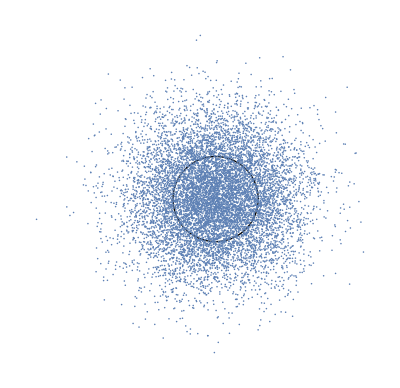

```mathematica
s = 1
NN = 10000
RandData = Table[{RandomVariate[NormalDistribution[0,s]],RandomVariate[NormalDistribution[0,s]]},{NN}];
X1 = Graphics[Circle[{0,0},1]];
X2 = ListPlot[RandData];
bullseyes=0;
For[i = 0, i < NN, i++; If[Norm[RandData[[i]]]<1,bullseyes++]]
Print["Number of bullseyes: ", bullseyes]
Show[X1,X2]
```

```mathematica
N[1-E^(-1/(50))]
```

0.0198013

5

10000

Number of bullseyes: 197

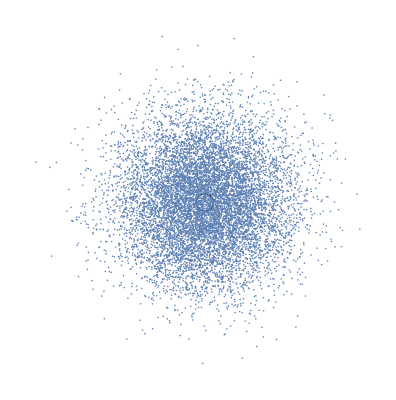

```mathematica
s = 5
NN = 10000
RandData = Table[{RandomVariate[NormalDistribution[0,s]],RandomVariate[NormalDistribution[0,s]]},{NN}];
X1 = Graphics[Circle[{0,0},1]];
X2 = ListPlot[RandData];
bullseyes=0;
For[i = 0, i < NN, i++; If[Norm[RandData[[i]]]<1,bullseyes++]]
Print["Number of bullseyes: ", bullseyes]
Show[X1,X2]
```

```mathematica
N[1-E^(-1/(0.5))]
```

0.864665

1/2

10000

Number of bullseyes: 8609

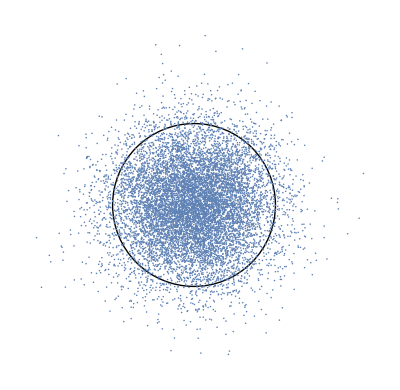

```mathematica
s = 1/2
NN = 10000
RandData = Table[{RandomVariate[NormalDistribution[0,s]],RandomVariate[NormalDistribution[0,s]]},{NN}];
X1 = Graphics[Circle[{0,0},1]];
X2 = ListPlot[RandData];
bullseyes=0;
For[i = 0, i < NN, i++; If[Norm[RandData[[i]]]<1,bullseyes++]]
Print["Number of bullseyes: ", bullseyes]
Show[X1,X2]
```